# Midterm Review - Continuous RV

## Continuous Random Variables

| Mean | Variance | PDF | CDF | MGF
Exponential | 1/β | 1/β^2 | Piecewise[{{β e^(-β x), x≥0}, {0, otherwise}}] | Piecewise[{{1-e^(-β x), x≥0}, {0, otherwise}}] | β/(β-t)
Gamma | α/β | α/β^2 | Piecewise[{{β^α/α x^(α-1) e^-βx, x>0}, {0, otherwise}}] | messy | (1-t/β)^-α
Chi Squared | γ | 2γ | Piecewise[{{1/(γ/2 2^(γ/2)) x^(γ/2-1)e^(-x/2), x>0}, {0, otherwise}}] | messy | (1-2 t)^(-γ/2)
Normal | μ | σ^2 | 1/(√(2 π) σ)e^(-1/2((x-μ)/σ)^2) | 1/2 erfc((μ-x)/(√2 σ)) | e^((σ^2 t^2)/2+μ t)
Standard Normal | 0 | 1 | 1/(√(2 π))e^(-1/2 x^2) | 1/2 erfc(-x/(√2)) | e^(t^2/2)
Weibull | μ_W | σ_W^2 | Piecewise[{{αβ x^(β-1)e^(-α x^β), x>0}, {0, otherwise}}] | messy | messy
Uniform | (a+b)/2 | 1/12 (b-a)^2 | Piecewise[{{1/(b-a), a≤x≤b}, {0, otherwise}}] | Piecewise[{{(x-a)/(b-a), a≤x≤b}, {1, x>b}}] | (ⅇ^(b t)-ⅇ^(a t))/(t (b-a))

μ_W=α^(-1/β) 1+1/β,σ_W^2=α^(-2/β) (1+2/β-(1+1/β)^2).

### Continuous Random Variable and its Properties

A continuous random variable is a map X:S→ℝ with a probability density function f_X:ℝ→ℝ such that

f_X(x)≥0 for all x∈ℝ,

∫_(-∞)^∞ f_X(x)ⅆx=1.

And the cumulative distribution function is defined as

F_X(x):=P[X≤ x]=∫_(-∞)^x f_X(y)ⅆy,

which implies that f_X(x)=F'_X(x).
The expectation has the similar properties,

E[X]:=∫_ℝ x f_X(x)ⅆx,E[φ∘X]=∫_ℝ φ(x) f_X(x)ⅆx.

And the variance is given similarly, Var[X]=E[(X-E[X])]^2=E[X^2]-E[X]^2.
The median M_X is a number such that P[X≤M_X]=0.5.
The mode is a number at which f_X is maximum.

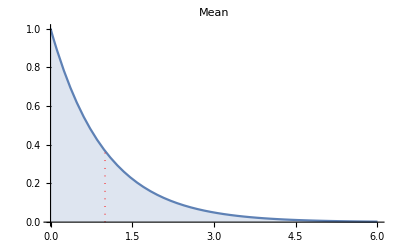
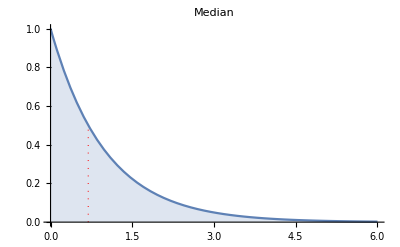
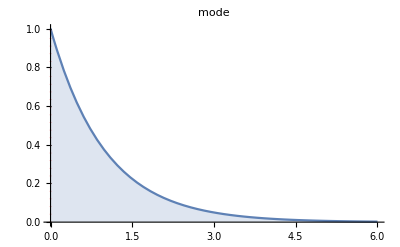

```mathematica
𝒟=ExponentialDistribution[1];
mode[D_]:=x/.Last[NMaximize[PDF[𝒟,x],x]]
Table[With[{m=f[𝒟]},Plot[PDF[𝒟,x],{x,0,6},PlotLabel->ToString[f],Filling->Axis,Epilog->{Directive[Red,Dotted,Thick],Line[{{m,0},{m,PDF[𝒟,m]}}]}]],{f,{Mean,Median,mode}}]
```

### Exponential Distribution

Purpose: time until first arrival?

Parameter and properties:

β>0 is the rate of arrival.

Mean | Variance | PDF | CDF | MGF
1/β | 1/β^2 | Piecewise[{{β e^(-β x), x≥0}, {0, otherwise}}] | Piecewise[{{1-e^(-β x), x≥0}, {0, otherwise}}] | β/(β-t)

The exponential distribution is memoryless, P[X>x+s|X>x]=P[X>s].

```mathematica
Manipulate[
Plot[PDF[ExponentialDistribution[β],x],{x,-1,5},
PlotRange->{0,5},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Exponential Distribution with β="<>ToString[β]
],{β,0.001,5},
Paneled->False]
```

Example:

##### Raindrops keep falling on my head at an average rate of 20 drops/min. What is the probability of having no raindrop falling on my head in a given 3 seconds time interval?

We can use β=1 (drop/3 seconds). The probability of no drop (success) in the first 3 seconds is

P[X>1]=1-∫_0^1 e^-x ⅆx=1-(1-1/e)=1/e=36.7%

Setting other values of β, such as β=20 (drops/min) and calculating P[X>1/20], will give the same result.

##### Given that no raindrop has fallen on my head in the past minute, what is the probability of having no raindrop on my head in another 3 seconds?

Still 36.7% due to the memoryless property.

### Gamma Distribution

Purpose: time until α^th arrival?

Parameter and properties:

α>0 is the number of arrivals you want.

β>0 is the rate of arrival.

Mean | Variance | PDF | MGF
α/β | α/β^2 | Piecewise[{{β^α/α x^(α-1) e^-βx, x>0}, {0, otherwise}}]     where Γ(α)=∫_0^∞ z^(α-1)e^-z ⅆz | (1-t/β)^-α

```mathematica
Manipulate[
Plot[PDF[GammaDistribution[α,1/β],x],{x,-1,5},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)" },
PlotLabel->"PDF of Gamma Distribution with α="<>ToString[α]<>", β="<>ToString[β]
],{α,0.001,5},{β,0.001,5},
Paneled->False]
```

### Chi-squared Distribution

Purpose: how is the sum of squares of γ independent standard normal random variables distributed?

Parameter and properties:

γ∈ℕ^+ is the degrees of freedom.

Mean | Variance | PDF | MGF
γ | 2γ | Piecewise[{{1/(γ/2 2^(γ/2)) x^(γ/2-1)e^(-x/2), x>0}, {0, True}}] | (1-2 t)^(-γ/2)

```mathematica
Manipulate[
Plot[PDF[ChiSquareDistribution[Floor[γ]],x],{x,-1,10},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","f_X(x)"},
PlotLabel->"PDF of Chi-squared Distribution with γ="<>ToString[Floor[γ]]
],{γ,1,10},
Paneled->False]
```

### Transformation of Random Variable

X is a continuous RV and φ:ℝ→ℝ is a strictly monotonic and differentiable function, then the PDF of Y=φ∘X is

f_Y(y)=Piecewise[{{f_X(φ^-1(y))·|(d φ^-1(y))/(d y)|, for y∈ran φ}, {0, otherwise}}]

### Normal Distribution

Purpose: not sure which distribution? Then normal distribution!

A Useful Conclusion: ∫_(-∞)^∞ e^(-x^2/c)ⅆx=√(c π), where c>0 is a constant.

Parameter and properties:

μ∈ℝ is the mean,

σ^2>0 is the variance

Mean | Variance | PDF | CDF | MGF
μ | σ^2 | 1/(√(2 π) σ)e^(-1/2((x-μ)/σ)^2) | 1/2 erfc((μ-x)/(√2 σ))       where  erfc(z):=1-2/(√π)∫_0^z e^(-t^2)ⅆt | e^((σ^2 t^2)/2+μ t)

Let X be normally distributed, then Z:=(X-μ)/σ has standard normal distribution (normal distribution with μ=0,σ=1).

```mathematica
Manipulate[
Plot[{PDF[NormalDistribution[μ,σ],x],CDF[NormalDistribution[μ,σ],x]},{x,-5,5},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x"},
PlotLegends->{"PDF","CDF"},
PlotLabel->"Normal Distribution with μ="<>ToString[μ]<>", σ^2="<>ToString[σ^2]
],{μ,-5,5},{σ,0.01,10},
Paneled->False]
```

Approximation of Binomial CDF: if Piecewise[{{n>10, if p is close to 1/2}, {n p>5, if p ≤1/2}, {n(1-p)>5, if p >1/2}}], the CDF at y∈ℕ can be approximated by normal distribution.
P[X≤y]=∑_(x=0)^y Binomial[n, x] (p^x(1-p))^(n-x)≈Φ((y+1/2-n p)/(√(n p(1-p))))

```mathematica
Manipulate[
Plot[{CDF[BinomialDistribution[n,p],x],CDF[NormalDistribution[],(x+1/2-n p)/(√(n p(1-p)))]},{x,-1,n},
PlotRange->{0,1},
Filling->Bottom,
AxesOrigin->{0,0},
ImageSize->300,
AxesLabel->{"x","F_X(x)"},
PlotLegends->{"CDF of Binomial Distribution\n with p="<>ToString[p]<>", n="<>ToString[n],"Φ（(x + 1/2 - n p)/(√(n p (1 - p))))"},
PlotLabel->"CDF of two distributions"
],{p,0.001,0.999},{n,{1,5,10,15,20}},
Paneled->False]
```

##### Example: For a random variable X that follows a binomial distribution with n=100,p=0.5, use normal approximation to calculate P[X≥40].

We have P[X≥40]=1-P[X<40]=1-P[X≤39]=1-Φ((39+1/2-100·0.5)/(√(100·0.5^2)))

```mathematica
1-CDF[NormalDistribution[],(39+1/2-100 0.5)/(√(100 0.5^2))]
```

0.982136

### Standard Normal Distribution

The standard normal distribution will enable you to find the value of CDF, Φ(x), simply by looking up the following table. There are many forms of standard normal table, and you can check them out here: https://en.wikipedia.org/wiki/Standard_normal_table. With the information we can calculate the following:

P[X≤a]=P[X<a]=Φ(a)

P[a≤X≤b]=P[X≤b]-P[X≤a]=Φ(b)-Φ(a)

```mathematica
TableForm[Table[CDF[NormalDistribution[],x+y],{y,Table[i,{i,0,35}]*0.1},{x,Table[i,{i,0,9}]*0.01}],TableHeadings->{Table[i,{i,0,40}]*0.1,Table[i,{i,0,9}]*0.01}]//Style[#,PrintPrecision->4,FontFamily->"Latin Modern Sans",FontSize->12]&
```

| 0. | 0.01 | 0.02 | 0.03 | 0.04 | 0.05 | 0.06 | 0.07 | 0.08 | 0.09
0. | 0.5 | 0.503989 | 0.507978 | 0.511966 | 0.515953 | 0.519939 | 0.523922 | 0.527903 | 0.531881 | 0.535856
0.1 | 0.539828 | 0.543795 | 0.547758 | 0.551717 | 0.55567 | 0.559618 | 0.563559 | 0.567495 | 0.571424 | 0.575345
0.2 | 0.57926 | 0.583166 | 0.587064 | 0.590954 | 0.594835 | 0.598706 | 0.602568 | 0.60642 | 0.610261 | 0.614092
0.3 | 0.617911 | 0.62172 | 0.625516 | 0.6293 | 0.633072 | 0.636831 | 0.640576 | 0.644309 | 0.648027 | 0.651732
0.4 | 0.655422 | 0.659097 | 0.662757 | 0.666402 | 0.670031 | 0.673645 | 0.677242 | 0.680822 | 0.684386 | 0.687933
0.5 | 0.691462 | 0.694974 | 0.698468 | 0.701944 | 0.705401 | 0.70884 | 0.71226 | 0.715661 | 0.719043 | 0.722405
0.6 | 0.725747 | 0.729069 | 0.732371 | 0.735653 | 0.738914 | 0.742154 | 0.745373 | 0.748571 | 0.751748 | 0.754903
0.7 | 0.758036 | 0.761148 | 0.764238 | 0.767305 | 0.77035 | 0.773373 | 0.776373 | 0.77935 | 0.782305 | 0.785236
0.8 | 0.788145 | 0.79103 | 0.793892 | 0.796731 | 0.799546 | 0.802337 | 0.805105 | 0.80785 | 0.81057 | 0.813267
0.9 | 0.81594 | 0.818589 | 0.821214 | 0.823814 | 0.826391 | 0.828944 | 0.831472 | 0.833977 | 0.836457 | 0.838913
1. | 0.841345 | 0.843752 | 0.846136 | 0.848495 | 0.85083 | 0.853141 | 0.855428 | 0.85769 | 0.859929 | 0.862143
1.1 | 0.864334 | 0.8665 | 0.868643 | 0.870762 | 0.872857 | 0.874928 | 0.876976 | 0.879 | 0.881 | 0.882977
1.2 | 0.88493 | 0.886861 | 0.888768 | 0.890651 | 0.892512 | 0.89435 | 0.896165 | 0.897958 | 0.899727 | 0.901475
1.3 | 0.9032 | 0.904902 | 0.906582 | 0.908241 | 0.909877 | 0.911492 | 0.913085 | 0.914657 | 0.916207 | 0.917736
1.4 | 0.919243 | 0.92073 | 0.922196 | 0.923641 | 0.925066 | 0.926471 | 0.927855 | 0.929219 | 0.930563 | 0.931888
1.5 | 0.933193 | 0.934478 | 0.935745 | 0.936992 | 0.93822 | 0.939429 | 0.94062 | 0.941792 | 0.942947 | 0.944083
1.6 | 0.945201 | 0.946301 | 0.947384 | 0.948449 | 0.949497 | 0.950529 | 0.951543 | 0.95254 | 0.953521 | 0.954486
1.7 | 0.955435 | 0.956367 | 0.957284 | 0.958185 | 0.95907 | 0.959941 | 0.960796 | 0.961636 | 0.962462 | 0.963273
1.8 | 0.96407 | 0.964852 | 0.96562 | 0.966375 | 0.967116 | 0.967843 | 0.968557 | 0.969258 | 0.969946 | 0.970621
1.9 | 0.971283 | 0.971933 | 0.972571 | 0.973197 | 0.97381 | 0.974412 | 0.975002 | 0.975581 | 0.976148 | 0.976705
2. | 0.97725 | 0.977784 | 0.978308 | 0.978822 | 0.979325 | 0.979818 | 0.980301 | 0.980774 | 0.981237 | 0.981691
2.1 | 0.982136 | 0.982571 | 0.982997 | 0.983414 | 0.983823 | 0.984222 | 0.984614 | 0.984997 | 0.985371 | 0.985738
2.2 | 0.986097 | 0.986447 | 0.986791 | 0.987126 | 0.987455 | 0.987776 | 0.988089 | 0.988396 | 0.988696 | 0.988989
2.3 | 0.989276 | 0.989556 | 0.98983 | 0.990097 | 0.990358 | 0.990613 | 0.990863 | 0.991106 | 0.991344 | 0.991576
2.4 | 0.991802 | 0.992024 | 0.99224 | 0.992451 | 0.992656 | 0.992857 | 0.993053 | 0.993244 | 0.993431 | 0.993613
2.5 | 0.99379 | 0.993963 | 0.994132 | 0.994297 | 0.994457 | 0.994614 | 0.994766 | 0.994915 | 0.99506 | 0.995201
2.6 | 0.995339 | 0.995473 | 0.995604 | 0.995731 | 0.995855 | 0.995975 | 0.996093 | 0.996207 | 0.996319 | 0.996427
2.7 | 0.996533 | 0.996636 | 0.996736 | 0.996833 | 0.996928 | 0.99702 | 0.99711 | 0.997197 | 0.997282 | 0.997365
2.8 | 0.997445 | 0.997523 | 0.997599 | 0.997673 | 0.997744 | 0.997814 | 0.997882 | 0.997948 | 0.998012 | 0.998074
2.9 | 0.998134 | 0.998193 | 0.99825 | 0.998305 | 0.998359 | 0.998411 | 0.998462 | 0.998511 | 0.998559 | 0.998605
3. | 0.99865 | 0.998694 | 0.998736 | 0.998777 | 0.998817 | 0.998856 | 0.998893 | 0.99893 | 0.998965 | 0.998999
3.1 | 0.999032 | 0.999065 | 0.999096 | 0.999126 | 0.999155 | 0.999184 | 0.999211 | 0.999238 | 0.999264 | 0.999289
3.2 | 0.999313 | 0.999336 | 0.999359 | 0.999381 | 0.999402 | 0.999423 | 0.999443 | 0.999462 | 0.999481 | 0.999499
3.3 | 0.999517 | 0.999534 | 0.99955 | 0.999566 | 0.999581 | 0.999596 | 0.99961 | 0.999624 | 0.999638 | 0.999651
3.4 | 0.999663 | 0.999675 | 0.999687 | 0.999698 | 0.999709 | 0.99972 | 0.99973 | 0.99974 | 0.999749 | 0.999758
3.5 | 0.999767 | 0.999776 | 0.999784 | 0.999792 | 0.9998 | 0.999807 | 0.999815 | 0.999822 | 0.999828 | 0.999835

Estimation: From the table you can read (how? which number in the table are you using?)

P[-σ<X-μ<σ]=0.68
P[-2σ<X-μ<2σ]=0.95
P[-3σ<X-μ<3σ]=0.997

```mathematica
CDF[NormalDistribution[0,1],1]//N
```

0.841345

Example:

##### A machine in the soft drink factory produces bottles of drinks with mean μ=500 mL and standard deviation σ=1 mL. How many mLs should a bottle have, so that 95% of the bottles produced by this machine have less drink than the bottle?

We need Z=(X-μ)/σ=(X-500)/1>1.65⇒X>501.65.

```mathematica
InverseCDF[NormalDistribution[500,1],0.95]
```

501.645

### Chebyshev Inequality

Purpose: To (roughly) estimate the variance of a random variable.

Mathematical representation: for k∈ℕ\{0}, P[|X|≥c]≤E[|X|^k]/c^k.

Application: P[|X-μ|≥m σ]≤1/m^2.

### Reliability

To study the reliability of a system, we have the following:

Failure density f(t)=lim_(Δt→0) P[t≤T≤t+Δt]/Δt, the probability of failing at time t, (uniform, Weibull, ...)

reliability function R(t)=1-F(t), the probability of system still working at time t,

hazard rate ρ(t)=lim_(Δt→0) P[t≤T≤t+Δt|T≥t]/Δt=(f(t))/(R(t)), the rate of failing at time t given that it didn’t fail before t.

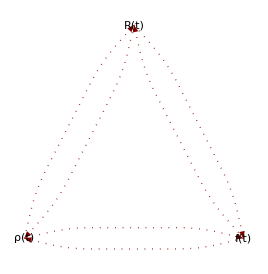

```mathematica
TreePlot[{{"R(t)"->"ρ(t)","ρ(t)=-(R'(t))/(R(t))"},{"ρ(t)"->"R(t)","R(t)=exp(-∫_0^t ρ(x)ⅆx)"},{"R(t)"->"f(t)","f(t)=-R '(t)"},{"f(t)"->"R(t)","R(t)=1-F(t)"},{"ρ(t)"->"f(t)","f(t)=ρ(t)R(t)"},{"f(t)"->"ρ(t)","ρ(t)=(f(t))/(1-F(t))"}},DirectedEdges->True,VertexLabeling->True,PlotStyle->Dotted] /.Inset[a_,b_,c_,d_,DIR_,opts__]:>Inset[a,b,c,d,opts,Background->White]
```

For series system, all components still working ⇒ system still working. R_S(t)=P[all components still working]=∏_(i=1)^k R_i(t).

For parallel system, at least one component still working ⇒ system still working. R_S(t)=P[not all components broken]=1-∏_(i=1)^k (1-R_i(t)).

Example:

##### Your professor has announced that we will have a quiz on Monday class (just an example! not real!), but you don’t know the exact time. What is the probability of not having a quiz in the first 45 minutes? Assume that a class is non-stop and 90 minutes long.

We can use uniform distribution to describe the “failure” density,

f(t)=Piecewise[{{1/90, if 0≤t≤90}, {0, otherwise}}]

And the reliability at time t=45 is

R(t)=1-F(t)=1-t/90=0.5

##### what is the expected rate of your professor giving the quiz at the very next moment?

The hazard rate at t=45 can be calculated as

ρ(t)=(f(t))/(1-F(t))=(1/90)/(1-t/90)=(1/90)/(1-45/90)=1/45

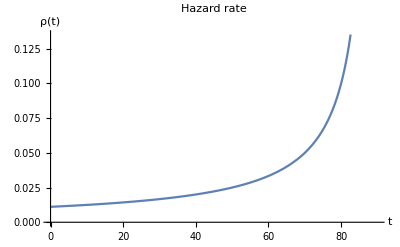

```mathematica
Plot[(1/90)/(1-t/90),{t,0,90},AxesOrigin->{0,0},AxesLabel->{"t","ρ(t)"},PlotLabel->"Hazard rate"]
```

### Weibull Distribution

Purpose: To represent a failure density f(t).

Parameters and properties:

α,β>0.

the hazard rate is Piecewise[{{constant, if β=1}, {increasing, if β>1}, {decreasing, if β<1}}].

Mean | Variance | PDF
α^(-1/β) 1+1/β | α^(-2/β) (1+2/β-(1+1/β)^2) | Piecewise[{{αβ x^(β-1)e^(-α x^β), x>0}, {0, True}}]

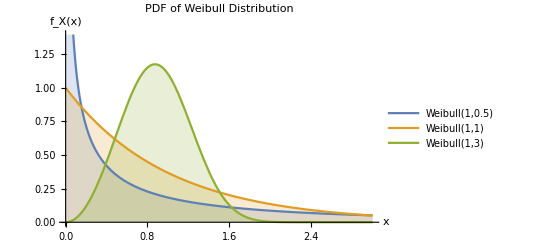

```mathematica
Plot[Table[PDF[WeibullDistribution[β,1^(-1/β)],x],{β,{0.5,1,3}}]//Evaluate,{x,0,3},Filling->Axis,PlotLegends->{"Weibull(1,0.5)","Weibull(1,1)","Weibull(1,3)"},AxesLabel->{"x","f_X(x)"},PlotLabel->"PDF of Weibull Distribution"]
```

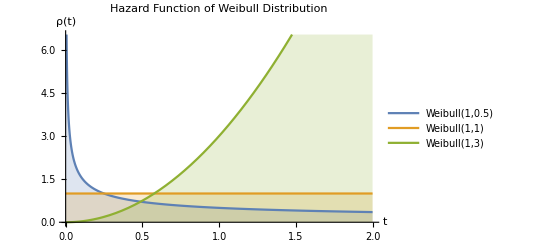

```mathematica
Plot[Table[HazardFunction[WeibullDistribution[β,1^(-1/β)],x],{β,{0.5,1,3}}]//Evaluate,{x,0,2},Filling->Axis,PlotLegends->{"Weibull(1,0.5)","Weibull(1,1)","Weibull(1,3)"},AxesLabel->{"t","ρ(t)"},PlotLabel->"Hazard Function of Weibull Distribution"]
```